```mathematica
Β=BR[4,{1,2,3,-1,-2,-1,-1}];
```

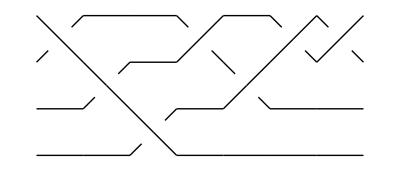

```mathematica
BraidPlot[Β]
```

```mathematica
M=Table[DifferentialAsMatrix[Β,r,MultispectralDifferential[β,γ]],{r,-5,4}];
```

```mathematica
M⟦{1,-1}⟧
```

{MatrixWrapper[0,{}],MatrixWrapper[0,{}]}

```mathematica
Clear[doSomething]
```

```mathematica
doSomething[doSomething[x_]]:=doSomething[x]
```

```mathematica
invertibleEntries[m_]:=Position[m,Except[0,x_?NumericQ],{2},1]
```

```mathematica
doSomething[{initial___,MatrixWrapper[r0_,m0_],MatrixWrapper[r1_,m1_],MatrixWrapper[r2_,m2_],final___}]/;Length[invertibleEntries[m1]]≥1:=Module[{i,j,x,mm,row,column},
{i,j}=invertibleEntries[m1]⟦1⟧;
(*Print[{Length[{initial}],i,j}];*)

x=m1⟦i,j⟧;
mm=Drop[Drop[m1,{i}],{},{j}];
row=Drop[m1⟦i⟧,{j}];
column=Drop[m1⟦All,j⟧,{i}];
(*Print[mm//MatrixForm];
Print[row];
Print[column];
Print[ x^-1 Outer[Times,column,row,1]//MatrixForm];*)

{initial,MatrixWrapper[r0,Drop[m0,{j}]],MatrixWrapper[r1-1,mm-x^-1 Outer[Times,column,row,1]],
MatrixWrapper[r2-1,Drop[m2,{},{i}]],final}
]
```

```mathematica
doStuff[X_]:=FixedPoint[doSomething,X]
```

```mathematica
R=DecomposeComplex[gaussianElimination[doStuff[M]⟦1⟧]];
```

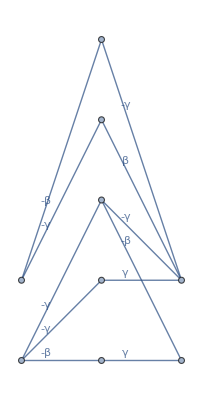
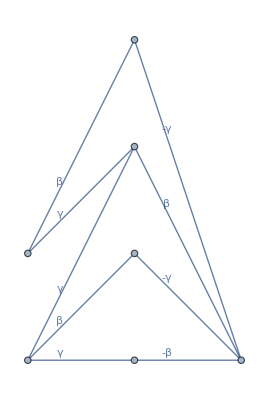

```mathematica
GraphComplex/@R
```

```mathematica
MatrixForm/@R⟦1,All,2⟧
```

{{},{},{},({}),(β
γ
0
0),(-γ | β | -β | 0
0 | 0 | -β | -γ),{},{},{},{}}

```mathematica
numberOfColumns[MatrixWrapper[c_,_]]:=c
numberOfRows[MatrixWrapper[_,m_]]:=Length[m]
```

```mathematica
TakeRowsAndColumns[m_MatrixWrapper,rows_,columns_]:=MatrixWrapper[Length[columns],m⟦2⟧⟦rows,columns⟧]
```

```mathematica
transpose[MatrixWrapper[c_,{}]]:=MatrixWrapper[0,Table[{},{c}]]
transpose[MatrixWrapper[_,m_]]:=MatrixWrapper[Length[m],Transpose[m]]
```

```mathematica
GraphAdjacencyMatrix[complex_]:=Module[{
rowSizes=(numberOfColumns/@complex)~Join~{numberOfRows[complex⟦-1⟧]},
columnSizes={numberOfColumns[complex⟦1⟧]}~Join~(numberOfRows/@complex),
},
ArrayFlatten[Table[
If[j==i+1,transpose[complex⟦i⟧]⟦2⟧,If[j==i-1,complex⟦j,2⟧,Table[0,{rowSizes⟦i⟧},{columnSizes⟦j⟧}]]]
 ,{i,Cases[Range[1,Length[complex]+1],k_/;rowSizes⟦k⟧>0]},{j,1,Length[complex]+1}]]
]
```

```mathematica
GraphComplex[complex_]:=Module[{columnSizes,partialSums,g},
columnSizes={numberOfColumns[complex⟦1⟧]}~Join~(numberOfRows/@complex);
g=WeightedAdjacencyGraph[GraphAdjacencyMatrix[complex]/.(0->∞)];
g=SetProperty[g,EdgeLabels->MapThread[#1->Placed[#2,0.3]&,{EdgeList[g],PropertyValue[g,EdgeWeight]}]];
g=SetProperty[g,VertexCoordinates->Flatten[Table[Table[{i,j},{j,1,columnSizes⟦i⟧}],{i,1,Length[columnSizes]}],1]]
]
```

```mathematica
DecomposeComplex[complex_]:=
Module[{
columnSizes={numberOfColumns[complex⟦1⟧]}~Join~(numberOfRows/@complex),
nonzeroToOne,
adjacencyMatrix,
components,
lookup,
partialSums,
objects,
summand
},
nonzeroToOne[0]=0;
nonzeroToOne[_]:=1;
adjacencyMatrix=GraphAdjacencyMatrix[complex];
adjacencyMatrix=Map[nonzeroToOne,adjacencyMatrix,{2}];
partialSums=FoldList[Plus,0,columnSizes];
lookup[k_]:=Module[{p},
p=Position[partialSums,n_/;n<k,1]⟦-1,1⟧;
{p,k-partialSums⟦p⟧}
];
components=ConnectedComponents[AdjacencyGraph[adjacencyMatrix]]/.k_Integer:>lookup[k];
objects[component_]:=Table[Cases[component,{d,k_}:>k],{d,1,Length[complex]+1}];
summand[component_]:=Module[{objs=objects[component]},
Table[
TakeRowsAndColumns[complex⟦i⟧,objs⟦i+1⟧,objs⟦i⟧]
,{i,1,Length[complex]}]
];
summand/@components
]
```

```mathematica
T={MatrixWrapper[2,{{a,a}}],MatrixWrapper[1,{{b}}],MatrixWrapper[1,{{0}}],MatrixWrapper[1,{{c}}]};
```

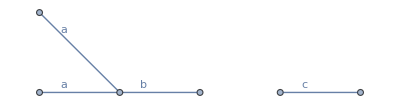

```mathematica
GraphComplex[T]
```

```mathematica
dimensions[MatrixWrapper[c_,m_]]:={Length[m],c}
```

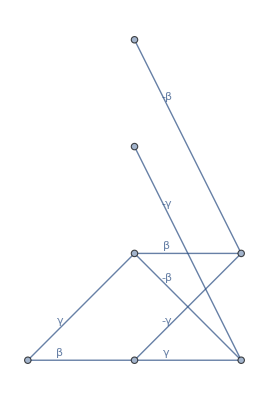
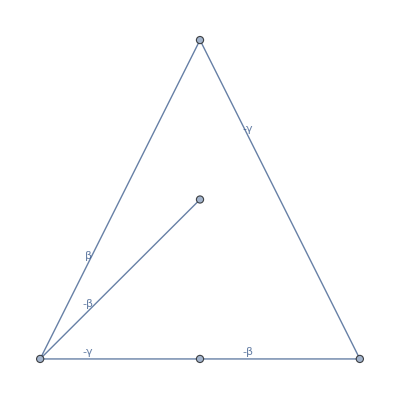
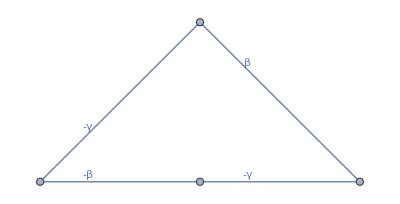

```mathematica
GraphComplex/@DecomposeComplex[R]
```

```mathematica
Unprotect[MatrixForm];
MatrixForm[m_MatrixWrapper]:=MatrixForm[m⟦2⟧]
```

```mathematica
MatrixForm/@DecomposeComplex[R]⟦1⟧
```

{{},{},{},({}),(β
γ
0
0),(γ | -β | -γ | 0
-γ | β | 0 | -β),{},{},{},{}}

```mathematica
gaussianElimination[complex_]:=Module[{zeroes,quotient,remainder,result1,result2,result=$Failed},
zeroes=Count[#⟦2⟧,0,{2}]&/@complex;
Do[
If[complex⟦i,2,j,l⟧=!=0∧complex⟦i,2,k,l⟧=!=0,
{{quotient},remainder}=PolynomialReduce[complex⟦i,2,j,l⟧,{complex⟦i,2,k,l⟧},{β,γ}];
If[remainder===0,
(*Print["Found a divisor: ",{i,j,k,l}];*)
result1=complex⟦i,2⟧;
result1⟦j⟧=result1⟦j⟧-quotient result1⟦k⟧;
If[Count[result1,0,{2}]>zeroes⟦i⟧,
If[numberOfRows[complex⟦i+1⟧]==0,
result=ReplacePart[complex,{{i,2}->result1}];
Break[],
result2=Transpose[complex⟦i+1,2⟧];
result2⟦j⟧=result2⟦j⟧+quotient result2⟦k⟧;
If[Count[result1,0,{2}]+Count[result2,0,{2}]≤zeroes⟦i⟧+zeroes⟦i+1⟧,
result2=Transpose[result2];
result=ReplacePart[complex,{{i,2}->result1,{i+1,2} ->result2}];
Break[]
]
]
]
]
]
,{i,1,Length[complex]},{j,1,numberOfRows[complex⟦i⟧]},{k,Complement[Range[numberOfRows[complex⟦i⟧]],{j}]},{l,1,numberOfColumns[complex⟦i⟧]}];
If[result===$Failed,
complex,
gaussianElimination[result]
]
]
```

```mathematica
MatrixForm/@DecomposeComplex[R]⟦1⟧
```

{{},{},{},({}),(β
γ
0
0),(γ | -β | -γ | 0
-γ | β | 0 | -β),{},{},{},{}}

```mathematica
GraphComplex[DecomposeComplex[R]⟦1⟧]
```

-Graphics-

```mathematica
gaussianElimination[DecomposeComplex[R]⟦1⟧]
```

{MatrixWrapper[0,{}],MatrixWrapper[0,{}],MatrixWrapper[0,{}],MatrixWrapper[0,{{}}],MatrixWrapper[1,{{β},{γ},{0},{0}}],MatrixWrapper[4,{{0,0,-γ,-β},{-γ,β,0,-β}}],MatrixWrapper[2,{}],MatrixWrapper[0,{}],MatrixWrapper[0,{}],MatrixWrapper[0,{}]}

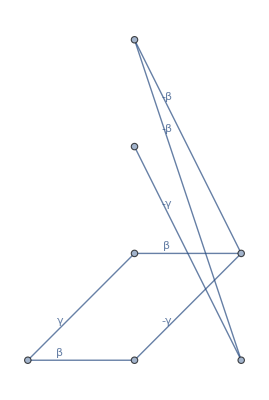

```mathematica
GraphComplex[%]
```